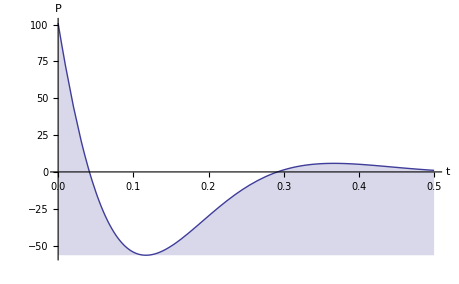

```mathematica
p=101;
a=9.1;
w=2π*2;
Plot[2p*(E^(-a x))*Cos[w x+π/3],{x,0,.5},Filling->Bottom,AxesLabel->{"t","P"},PlotRange->Full]
```

```mathematica
*
```

```mathematica
Clear[p,a,w]
```

```mathematica
Manipulate[Plot[2p*(E^(-a x))*Cos[w x+π/3],{x,0,z},PerformanceGoal->"Quality",Filling->Bottom,AxesLabel->{"t","P"}],{z,0.11,1},{p,1,101},{a,1,9.1*10^5},{w,0,2π*20.3}]
```

```mathematica
f[.000001]
```

40.6181

```mathematica
Reduce[202 ⅇ^(-910000. x) Sin[π/6-523.3893360880595 x]==0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈Integers&&(x==0.0010004-0.0120048 C[1]||x==0.0010004-0.00191062 (3.14159+6.28319 C[1]))

```mathematica
Expand[(x-1)(x+1)(x-5)(x+7)x]
```

35 x-2 x^2-36 x^3+2 x^4+x^5